```mathematica
{name, first} = Transpose[Import["C:\\Users\\Ivan\\Documents\\Учеба\\Диплом\\Данные\\name.dat", "Table"]] ;
name
first
```

{stp0,stp2,stp4,srp1,srp2,srp3,srp4,srp5,srp6,srp7,srp8,srp9,sip1,sip2,srp10,srp11,srp12,srp13,srp14,srp15,srp16,srp17,sep5,sep4,sep3,sep1,sep0,nep0,nep1,nep3,nep4,nep5,nrp17,nrp16,nrp15,nrp14,nrp13,nrp12,nrp11,nrp10,nip3,nip1,nrp9,nrp8,nrp7,nrp6,nrp5,nrp4,nrp3,nrp2,nrp1,ntp4,ntp2,ntp0}

{9,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,9,9,9,9,9,9,8,8,8,8,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9}

```mathematica
k=IntegerString[#, 10, 2] & /@ Range[10]
```

{01,02,03,04,05,06,07,08,09,10}

```mathematica
(* Load experiment data *)
ClearAll[load] ;
load[id_] := Block[
	{prefix},
	prefix = StringTemplate["C:\\Users\\Ivan\\Documents\\Учеба\\Диплом\\Данные\\`1`-n450-2000-10000-"][IntegerString[id, 10, 2]] ;
	Table[
		Take[N[Import[StringTemplate["`1``2`.dat"][prefix, name[[i]]], "CSV"]], {first[[i]]+1, first[[i]]+1 + 1023}],
		{i, 1, 54}
	]
] ;
dataExp = load[1] ;
```

```mathematica
(* Load model data *)
dataModel = Import["C:\\Users\\Ivan\\Downloads\\vepp.dat", "Table"];
```

```mathematica
(* Load New model data *)
dataModelNew = Import["C:\\Users\\Ivan\\Downloads\\vepp4m.dat", "Table"];
```

```mathematica
(* Set optics data (all elements) *)
dataTwiss=Import["C:\\Users\\Ivan\\Documents\\Учеба\\Диплом\\Данные\\01-n450-2000-10000-twiss.dat","CSV"];
bx = dataTwiss[[All, 4]] ;
ax = dataTwiss[[All, 2]] ;
by = dataTwiss[[All, 8]] ;
ay = dataTwiss[[All, 6]];
fx=dataTwiss[[All, 3]];
```

```mathematica
(* Process data (optics at BPMs) *)
data$bpm = Cases[Rest[dataModel], {"MARK", __}] ;

(* Formal ideal model data *)
bpm$count    = Length[data$bpm]-1                (* -- number of unique BPMs *)
bpm$name     = data$bpm[[All, 2]] // Most ;           (* -- list of BPM names *)
bpm$position = data$bpm[[All, 3]] // Most ;           (* -- list of BPM positions *)
bpm$bx       = data$bpm[[All, 4]] // Most ;  
Length[bpm$bx ]               (* -- bx values at BPMs *)
bpm$ax       = data$bpm[[All, 5]] // Most ;           (* -- ax values at BPMs *)
bpm$fx       = Differences[data$bpm[[All, 6]]] ; 
Length[bpm$fx]                                        (* -- x phase advance between BPMs *)
bpm$by       = data$bpm[[All, 7]] // Most ;           (* -- by values at BPMs *)
bpm$ay       = data$bpm[[All, 8]] // Most ;           (* -- ay values at BPMs *)
bpm$fy       = Differences[data$bpm[[All, 9]]] ;      (* -- y phase advance between BPMs *)
```

54

54

54

```mathematica
(* window function *)
ClearAll[S$COSINE$WINDOW] ;
S$COSINE$WINDOW::usage = "
S$COSINE$WINDOW[ORDER,LENGTH] -- generate cosine window data of order <ORDER> (integer) and window length <LENGTH> (integer)
" ;
S$COSINE$WINDOW[                    (* -- GENERATE COSINE WINDOW DATA (LIST) *)
  ORDER_?NumericQ,                  (* -- WINDOW ORDER (INTEGER/REAL) *)
  LENGTH_Integer                    (* -- WINDOW LENGTH (INTEGER) *)
] := If[
  SameQ[N[ORDER],N[0]],
  N[ConstantArray[1,LENGTH]],
  Times[
    Power[Plus[1,1],ORDER],
    Power[Factorial[ORDER],Plus[1,1]],
    Power[Factorial[Times[Plus[1,1],ORDER]],Subtract[0,1]],
    Power[Plus[1,Cos[Times[Plus[1,1],Pi,Subtract[Divide[Subtract[N[Range[LENGTH]],1],LENGTH],Divide[1,Plus[1,1]]]]]],ORDER]
  ]
] /; And[
  GreaterEqual[ORDER,0],
  GreaterEqual[LENGTH,1]
] ;
```

```mathematica
ClearAll[CalculateFreq];
CalculateFreq[sig_,pad_]:=Block[
{res,max,len,sig1,dat,pos,bin,amp,fun,x,fra,sigm},
len=Length[sig];
sigm=sig-Mean[sig];
sig1 = sigm*S$COSINE$WINDOW[1,len] ;
(*sig1 = PadRight[sig1, pad] ; *)
amp = Take[Abs[Fourier[sig1]],pad/2] ;
bin = First[Flatten[Position[amp,Max[Take[amp,-pad/2+2]]]]] ;

res = N[1/pad*(bin-1)];
(* fractional fourier and max bin of fractional fourier *)
fra = Abs[Fourier[sig1*Exp[2*Pi*I*(bin-2)*N[Range[0,pad-1]]/pad], FourierParameters->{0,2/pad}]];
max = Position[fra, Max[fra]] // Flatten // First;

res = N[1/pad*(bin-2)] + N[1/pad^2*2*(max-1)];

pos = max + Range[-10,10] ;
dat = {pos,Log10[fra[[pos]]]} // Transpose ;


fun = Interpolation[dat, InterpolationOrder -> 4 ] ;


max = x /. Last[FindMaximum[fun[x],{x,max-1,max+1}] // Quiet];
res = N[1/pad*(bin-2)] + N[1/pad^2*2*(max-1)]

]
```

```mathematica
ClearAll[calculateAmplandPhase];
calculateAmplandPhase[sig_,freqMid_]:=Block[
{ pad, WF, sumWF , c, s, ampl, phase,sig1},
sig1= sig - Mean[sig] ; (*Table[sig[[i]]-Mean[sig],{i,1,Length[sig]}];*)

WF=S$COSINE$WINDOW[0,Length[sig1]];
sumWF=Sum[WF[[i]],{i,Length[sig1]}];

c=(2/sumWF)*Sum[sig1[[i]]*WF[[i]]*Cos[2*Pi*freqMid*i],{i,Length[sig1]}];
s=(2/sumWF)*Sum[sig1[[i]]*WF[[i]]*Sin[2*Pi*freqMid*i],{i,Length[sig1]}];

ampl=Sqrt[c^2+s^2];
phase=ArcTan[c, s];
{ampl,phase,freqMid}
]
```

```mathematica
(* beta from ampl *)
ClearAll[betaFromAmpl];
betaFromAmpl[amplAndPhaseData_,betaModelMassive_]:=Block[
{ActionTheor,betaFromAmpl},
ActionTheor=Sum[(amplAndPhaseData[[i]][[1]])^2/(2*betaModelMassive[[i]]),{i,1,Length[amplAndPhaseData]}]/Length[amplAndPhaseData];
betaFromAmpl=Table[(amplAndPhaseData[[i]][[1]])^2/(2*ActionTheor),{i,1,Length[amplAndPhaseData]}]
]
```

```mathematica
(* Beta from phase *)
ClearAll[betaFromPhase];
betaFromPhase[amplAndPhaseData_,betaModel_,theorPhase_]:=Block[
{betaModelp,DeltPhaseExpp,theorPhasep,betaFromPhase1,DeltPhaseEx,betaFromPhaseMassive,DeltPhaseExp,deltPhaseExp9$11,deltPhaseTheor9$11,bet9,bet11},
betaModelp=Join[{betaModel[[54]]},betaModel,{betaModel[[1]]}];
Length[betaModelp];
DeltPhaseExp = Table[Mod[amplAndPhaseData[[Mod[id+1, 54, 1], 2]] - amplAndPhaseData[[id, 2]] - If[id == 1, amplAndPhaseData[[1, 3]]*2*Pi, 0]- If[id == 33, amplAndPhaseData[[1, 3]]*2*Pi, 0]+ If[id == 36, amplAndPhaseData[[1, 3]]*2*Pi, 0], 2*Pi, -Pi],{id, 1, 54}] ;
(*DeltPhaseExp=Table[amplAndPhaseData[[i+1]][[2]]-amplAndPhaseData[[i]][[2]],{i,1,Length[amplAndPhaseData]-1}];*)
DeltPhaseExpp=Join[{DeltPhaseExp[[54]]},DeltPhaseExp];
Length[DeltPhaseExpp];
theorPhasep=Join[{theorPhase[[54]]},theorPhase];
Length[theorPhasep];
betaFromPhase1=Table[Abs[betaModelp[[i]]*(Cot[DeltPhaseExpp[[i-1]]]+Cot[DeltPhaseExpp[[i]]])/(Cot[theorPhasep[[i-1]]]+Cot[theorPhasep[[i]]])],{i,2,bpm$count+1,1}];
betaFromPhase1[[10]]="non";
deltPhaseExp9$11=amplAndPhaseData[[11,2]]-amplAndPhaseData[[9,2]];
deltPhaseTheor9$11=theorPhase[[9]]+theorPhase[[10]];
bet9=Abs[betaModelp[[10]]*(Cot[DeltPhaseExpp[[9]]]+Cot[deltPhaseExp9$11])/(Cot[theorPhasep[[9]]]+Cot[deltPhaseTheor9$11])];
bet11=Abs[betaModelp[[12]]*(Cot[deltPhaseExp9$11]+Cot[DeltPhaseExpp[[12]]])/(Cot[deltPhaseTheor9$11]+Cot[theorPhasep[[12]]])];
betaFromPhase1=ReplacePart[betaFromPhase1,{9->bet9,11->bet11}]
(*betaFromPhase=Table[betaFromPhase1[[i]][[2]][[1]],{i,1,Length[betaFromPhase1]}]*)
(*betaFromPhase1=Table[{{Abs[betaModelp[[i]]*(Cot[DeltPhaseExpp[[i-2]]]-Cot[DeltPhaseExpp[[i-1]]+DeltPhaseExpp[[i-2]]])/(Cot[theorPhasep[[i-2]]]-Cot[theorPhasep[[i-1]]+theorPhasep[[i-2]]])]},{Abs[betaModelp[[i]]*(Cot[DeltPhaseExpp[[i-1]]]+Cot[DeltPhaseExpp[[i]]])/(Cot[theorPhasep[[i-1]]]+Cot[theorPhasep[[i]]])]},{Abs[betaModelp[[i]]*(Cot[DeltPhaseExpp[[i+1]]]-Cot[DeltPhaseExpp[[i+1]]+DeltPhaseExpp[[i]]])/(Cot[theorPhasep[[i+1]]]-Cot[theorPhasep[[i+1]]+theorPhasep[[i]]])]}},{i,3,bpm$count+2,1}];*)
(*betaFromPhaseMassive=Join[{{betaFromPhase1[[1]][[3]]}},{{betaFromPhase1[[2]][[2]],betaFromPhase1[[2]][[3]]}},Table[betaFromPhase1[[i]],{i,3,Length[betaFromPhase1]-2}],{{betaFromPhase1[[Length[betaFromPhase1]-1]][[1]],betaFromPhase1[[Length[betaFromPhase1]-1]][[2]]}},{{betaFromPhase1[[Length[betaFromPhase1]]][[1]]}}]*)
]
```

```mathematica
(* Calculate Signal  *)
(* X:k=1;  Y:k=2*)
signalProc[data_,k_,len_]:=Block[
{signal,midlefreq,Ampl},
signal=Table[data[[i]][[j]][[k]],{i,1,Length[data]},{j,1,Length[data[[1]]]}];
midlefreq=Mean[Table[CalculateFreq[Drop[signal,{10,10}][[i]],Length[signal[[i]]]],{i,1,Length[signal]-1}]];
Ampl=Table[calculateAmplandPhase[data[[i, 1;;len, k]],midlefreq],{i,1,Length[signal]}]

]
```

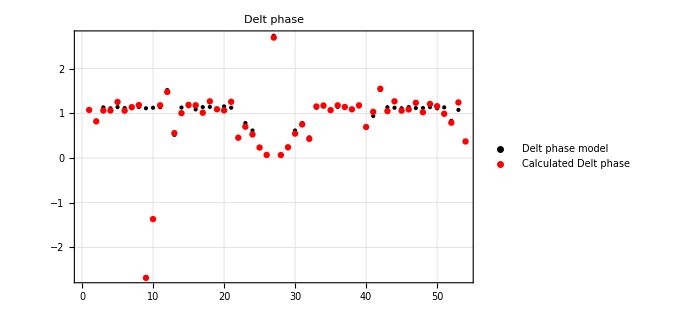
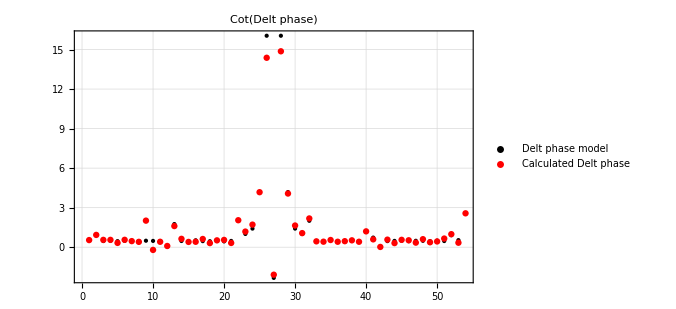
-Graphics- | -Graphics-

```mathematica
tmpX = Table[
	{ 
	bpm$fx[[id]],
		Mod[tmp[[Mod[id+1, 54, 1], 2]] - tmp[[id, 2]] -If[id == 1, tmp[[1, 3]]*2*Pi, 0]-If[id == 33, tmp[[1, 3]]*2*Pi, 0]+If[id == 36, tmp[[1, 3]]*2*Pi, 0], 2*Pi, -Pi],
		
	},
	{id, 1, 54}
] ;
{ListPlot[Transpose[tmpX], PlotRange->All, PlotStyle->{Directive[PointSize[Large], Black], Red},PlotTheme->"Detailed",PlotLegends->{"Delt phase model","Calculated Delt phase"},ImageSize -> 500,PlotLabel->"Delt phase"],
ListPlot[Cot[Transpose[tmpX]], PlotRange->All, PlotStyle->{Directive[PointSize[Large], Black], Red},PlotTheme->"Detailed",PlotLegends->{"Delt phase model","Calculated Delt phase"},ImageSize -> 500,PlotLabel->"Cot(Delt phase)"]
}//List//Grid
```

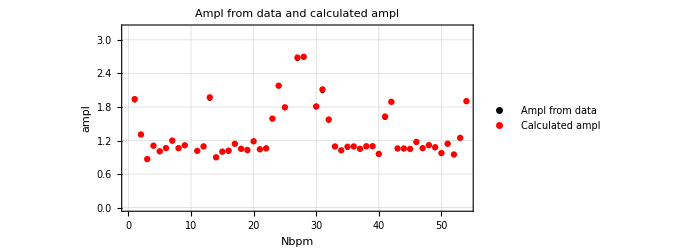
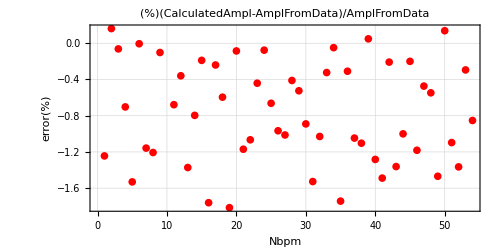
-Graphics- | -Graphics-

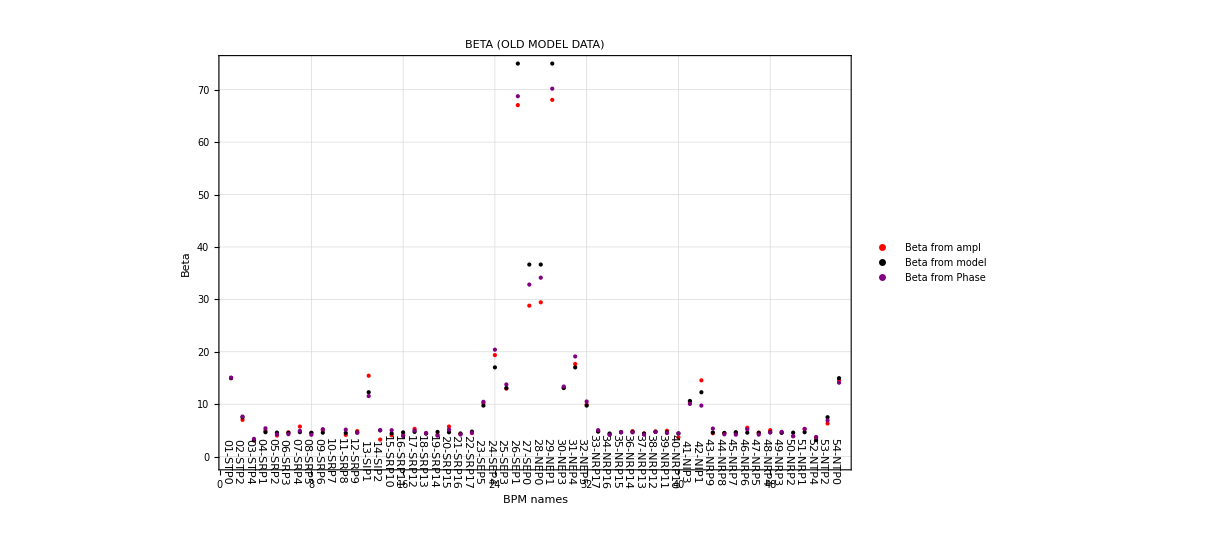

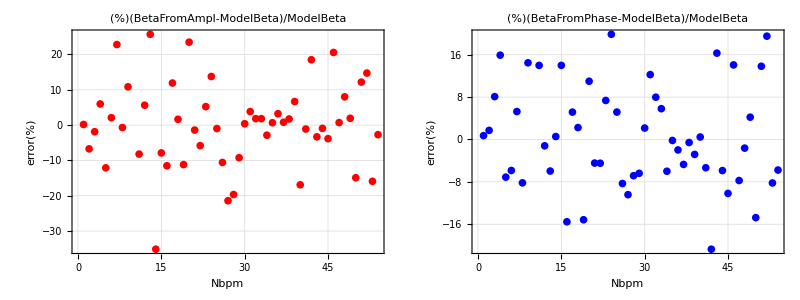

```mathematica
tmp=signalProc[dataExp,1,128];

nBPM=Drop[Table[i,{i,54}],{10,10}];
betaFromPhaseX=betaFromPhase[tmp,bpm$bx,bpm$fx];
betaXFromAmpl=Table[{nBPM[[i]],betaFromAmpl[Drop[tmp,{10,10}],Drop[bpm$bx ,{10,10}]][[i]]},{i,1,Length[nBPM]}];
ModelBetAndBetaFromAmpl=Table[{nBPM[[i]],(betaXFromAmpl[[i]][[2]]-Drop[bpm$bx ,{10,10}][[i]])/Drop[bpm$bx ,{10,10}][[i]]*100},{i,1,Length[nBPM]}];
(********************************************************************************************************************)
{
ListPlot[{tmp[[All, 1]], ax},PlotStyle->{Directive[PointSize[Large], Black], Red},PlotTheme->"Detailed",PlotLabel->"Ampl from data and calculated ampl", AspectRatio->1/2, ImageSize->500, FrameLabel->{"Nbpm", "ampl"}, PlotLegends->{"Ampl from data","Calculated ampl"}],
ListPlot[Table[{nBPM[[i]],(Drop[tmp[[All, 1]],{10,10}][[i]]-Drop[ax,{10,10}][[i]])/Drop[ax,{10,10}][[i]]*100},{i,1,Length[nBPM]}],PlotStyle->Red,PlotTheme->"Detailed",PlotLabel->"(%)(CalculatedAmpl-AmplFromData)/AmplFromData", AspectRatio->1/2, ImageSize->500, FrameLabel->{"Nbpm", "error(%)"}]

}//List//Grid

plotBetaX=Show[ListPlot[betaXFromAmpl,PlotTheme->"Detailed",PlotStyle->Directive[PointSize[Medium], Red],PlotLegends->{"Beta from ampl"}]];
plotBetaModelX=Show[ListPlot[Table[{nBPM[[i]],Drop[bpm$bx,{10,10}][[i]]},{i,1,Length[nBPM]}],PlotTheme->"Detailed",PlotStyle->Directive[PointSize[Medium], Black],PlotLegends->{"Beta from model"}]];
plotBetaRealX=Show[ListPlot[bx,PlotTheme->"Detailed",PlotStyle->Directive[PointSize[Medium], Green],PlotLegends->{"Beta real"}]];
plotBetaPhaseX=Show[ListPlot[betaFromPhaseX,PlotTheme->"Detailed",PlotStyle->Directive[PointSize[Medium], Purple],PlotLegends->{"Beta from Phase"}]];
plot$bpm = Graphics[
	Table[
		Style[
			Text[
				Rotate[StringTemplate["`2`-`1`"][bpm$name[[id]], IntegerString[id, 10, 2]], -90 Degree],
				{id, -1},
				{0, 1}
			],
			8
		],
		{id, 1, bpm$count}
	]
] ;
plot$beta = Show[
	plotBetaX, 
	plotBetaModelX,
plot$bpm ,
plotBetaPhaseX,
PlotRange->{All, {-10, All}},PlotLabel->"BETA (OLD MODEL DATA)",FrameLabel->{"BPM names", "Beta"},
	ImageSize -> 900
] 
{
ListPlot[ModelBetAndBetaFromAmpl,PlotStyle->Red,PlotTheme->"Detailed",PlotLabel->"(%)(BetaFromAmpl-ModelBeta)/ModelBeta", AspectRatio->1/2, ImageSize->500, FrameLabel->{"Nbpm", "error(%)"},PlotRange->All],
ListPlot[(betaFromPhaseX-bpm$bx)/bpm$bx*100,PlotStyle->Blue,PlotTheme->"Detailed",PlotLabel->"(%)(BetaFromPhase-ModelBeta)/ModelBeta", AspectRatio->1/2, ImageSize->500, FrameLabel->{"Nbpm", "error(%)"}]
}//List//Grid
(********************************************************************************************************************)
```